```mathematica
(*
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

PARAMETROS Y ADIMENSIONALIZACION  del modelo Morris Lecard tipo II

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)


ϕ=0.067;
gCa=4;
V3=12;
V4=17.4;
ECa=120;
EK=-84;
El=-60;
gK=8;
gL=2;
V1=-1.2;
V2=18;
Cm=20;
```

```mathematica
Eadim=-El;
gadim=gL;
```

```mathematica
g1=gK/gadim;
g2=gCa/gadim;
g3=gL/gadim;
u1=EK/Eadim;
u2=ECa/Eadim;
u3=El/Eadim;
```

```mathematica
λ=Cm/gadim;



a1=Eadim/V4;
b1=-V3/V4
a2=Eadim/V2;
b2=-V1/V2;
c=(1/(ϕ*λ));
cfast=0.1*c;
```

-0.689655

```mathematica
(*Functions*)

(*Relevant functions*)


minf[u_]:=0.5*(1+Tanh[a2 u+b2])
ninf[u_,b1_]:=0.5*(1+Tanh[a1 u+b1])
tau[u_,b1_]:=c/Cosh[(a1 u+b1)/2]



(*Derivatives*)

Dninf[u_,b1_]:=0.5* a1 Sech[b1+a1 u]^2
Dminf[u_]:=0.5* a2 Sech[b2+a2 u]^2

(*f function and derivative*)
f[u_,b1_]:=g1*ninf[u,b1]*(u-u1)+g2*minf[u]*(u-u2)+g3(u-u3)
Df[u_,b1_]:=g1*ninf[u,b1]+g2*minf[u]+g3+g1*Dninf[u,b1]*(u-u1)+g2*Dminf[u]*(u-u2)
```

```mathematica
β1[u_,b1_]:=-Dninf[u,b1]
M1[u_]:=g1 (u-u1)
```

```mathematica
b[ω_,u_,b1_]:=1-(M1[u] β1[u,b1] tau[u,b1])/(1+ (tau[u,b1]ω)^2)
a[ω_,u_,b1_]:=(M1[u] β1[u,b1] tau[u,b1]^2)/(1+ (tau[u,b1]ω)^2)
f1[ω_,u_,b1_]:=b[ω,u,b1]/a[ω,u,b1]
f2[ω_,u_,b1_]:=-Df[u,b1]/a[ω,u,b1]
Z[ω_,u_]:=Sqrt[1/(ω^2b[ω,u,b1]^2+(ω^2  a[ω,u,b1]-f2[ω,u,b1])^2)]
Zaprox[ω_,u_,b1_]:=Sqrt[(ω^2+f1[0,u,b1]^2)/(ω^2f1[0,u,b1]^2+(ω^2-f2[0,u,b1])^2)]
```

```mathematica
(*Linear Matrix*)
L[U_,B_]:={D[eq1[u,x1],{{u,x1}}],D[eq2[u,x1],{{u,x1}}]}/. {u->U,x1->0,Iny->f[U,B],B1->B}

(*EigenValues*)
Eigen[U_,B_]:=Eigenvalues[L[U,B]]
```

```mathematica
(*Dynamical system*)
tmin=50;
period=100;
tsim=200;
fmax=1;
amp=0.1;
I0=0;
```

```mathematica
eq1[t_,u_,x_]:=I0+ amp Sin[2 Pi t]Boole[t>tmin&&t<tmin+period]-f[u,b1]-g1*x*(u-u1);

eq2[t_,u_,x_]:=-x/tau[u,b1]-Dninf[u,b1]*eq1[t,u,x];
```

```mathematica
data2=NDSolve[{u'[t]==eq1[t,u[t],x[t]],x'[t]==eq2[t,u[t],x[t]],{u[0]==-1,x[0]==0}},{u[t],x[t]},{t,0,tsim}];
myu=Flatten[Table[u[t]/.data2,{t,0,tsim,0.01}]];
```

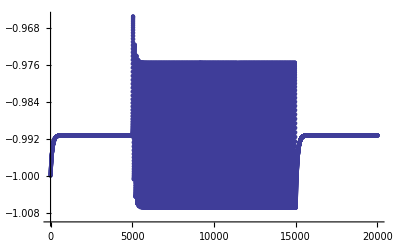

```mathematica
ListPlot[myu]
```

```mathematica
Manipulate[Show[Plot[Z[w,u],{w,0,100}],ListLinePlot[Abs[Fourier[myu]],PlotRange->All,Frame->True,ImageSize->500]],{u,-1,0}]
```

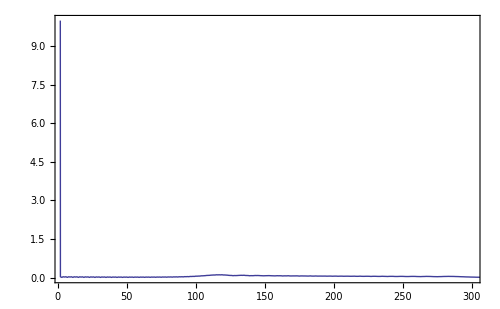

```mathematica
ListLinePlot[Abs[Fourier[myu]],PlotRange->{{4,300},{0,10}},Frame->True,ImageSize->500]
```